```mathematica
A = Import["C:\Users\david\Documents\GitHub\Chart_Comparisons\Seeded_Values_for_Comparison_Project.csv", {"Data", All, 2}]
```

{37,7,26,27,91,77,58,87,58,13,62,91,18,18,23,61,90,26,2,54,27,30,52,39,3,37,32,43,28,6,50,50,71,45,37,19,84,61,46,51,39,95,16,27,28,89,54,98,98,61}

```mathematica
B = Import["C:\Users\david\Documents\GitHub\Chart_Comparisons\Seeded_Values_for_Comparison_Project.csv", {"Data", All, 3}]
```

{25,88,65,5,28,51,29,83,10,98,52,26,68,64,3,6,39,53,96,15,40,24,65,27,84,13,83,43,14,65,76,95,15,100,5,62,92,58,10,32,9,83,41,99,46,32,19,1,13,39}

```mathematica
line1= Fit[A,{1,x},x]
line2= Fit[B,{1,x},x]
```

38.2318+0.337575 x

48.8522-0.12048 x

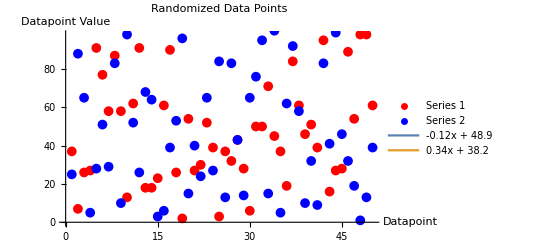

```mathematica
scatterplot = Show[ListPlot[Legended[A,"Series 1"], PlotMarkers->{Automatic, Medium}, PlotStyle->Red], ListPlot[Legended[B,"Series 2"], PlotMarkers->{Automatic, Medium}, PlotStyle->Blue],Plot[{Legended[line2, "-0.12x + 48.9"],Legended[line1, "0.34x + 38.2"]},{x,0,50}],AxesLabel->{HoldForm[Datapoint],HoldForm[Datapoint Value]},PlotLabel->RawBoxes[RowBox[{RowBox[{"Randomized"," ","Data"," ","Points"}]}]],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["MathematicaScatterplotExport.svg",scatterplot,ImageResolution->2000]
```

MathematicaScatterplotExport.svg

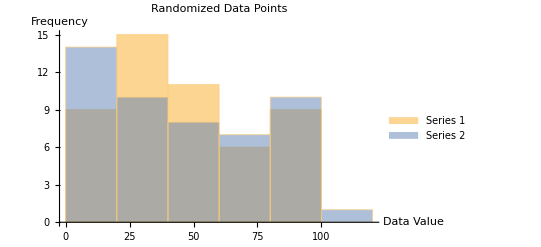

```mathematica
H = Histogram[{Legended[A,"Series 1"],Legended[B,"Series 2"]},AxesLabel->{HoldForm[Data Value],HoldForm[Frequency]},PlotLabel->RawBoxes[RowBox[{RowBox[{"Randomized"," ","Data"," ","Points"}]}]],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["MathematicaHistogram.svg",H,ImageResolution->2000]
```

MathematicaHistogram.svg